# Dynamica Tutorial Randall D. Beer Cognitive Science Program Indiana University Bloomington, IN 47406 rdbeer@indiana.edu Version 1.0.11 - 5/8/2021 Copyright (c) 1993-2021 Randall D. Beer. All rights reserved.

## Version History

5/8/2021 - Version 1.0.11 released

9/14/2020 - Version 1.0.10 released

7/31/18 - Version 1.0.9 released

8/20/16 - Version 1.0.8 released

8/1/16 - Version 1.0.7 released

8/8/14 - Version 1.0.6 released

12/6/11 - Version 1.0.5 released

8/2/10 - Version 1.0.4 released

10/31/08 - Version 1.0.2 released

9/1/08 - Version 1.0: First public release

## Introduction

In lieu of documentation, this notebook provides a tutorial to demonstrate some of the major capabilities of Dynamica, a Mathematica package for the analysis of smooth dynamical systems. For best results, you should evaluate each expression in the order it appears in the notebook because sometimes later ones depend on the results of earlier ones.  Feel free to experiment with different options to get a feel for how the various commands work. To see the full set of options for any Dynamica command, use Mathematica's Options function on the corresponding symbol.

Acknowledgments: Thanks to Chris Buckley, Hillel Chiel and Eduardo Izquierdo for providing feedback on an earlier version of this tutorial.

## Load Dynamica

Change this path to the  location of the Dynamica package on your machine.

```mathematica
<<"~rdbeer/Mathematica/Dynamica/Dynamica.m"
```

Dynamica (Version 1.0.10 - 9/14/2020), Copyright(c) 1993-2020 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## 1D Cubic System

A dynamical system is defined by specifying a list of righthand sides for each of its differential equations, a list of its state variables and their ranges of interest, and a list of its parameters and their ranges of interest. Below is the definition for the classic cubic system ẋ=-x^3+d x +c.

```mathematica
CS1=DynamicalSystem[{-x^3+d x+c} ,{{x,-5,5}},{{c,-5,5},{d,-5,5}}]
```

DynamicalSystem[«1 ODE»,{x},{c,d}]

The parameters of a dynamical system can be set or changed using standard Mathematica replacement rules.  The following expression makes a copy of the dynamical system that we defined above with c and d set to 0 and 5, respectively, and then reassigns the symbol CS1 to this copy .

```mathematica
CS1=CS1/.{c->0,d->5}
```

DynamicalSystem[«1 ODE»,{x},{c→0,d→5}]

The DisplayVectorField command does exactly what it says.

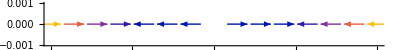

```mathematica
DisplayVectorField[CS1]
```

We can display trajectories of a dynamical system using the function DisplayTrajectories and specifying a list of initial conditions and a duration of time for which to integrate them.

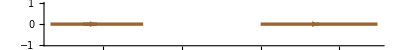

```mathematica
DisplayTrajectories[CS1,{{0.001},{-4}},2]
```

The DisplayFlow command displays a representative set of trajectories that give an overall picture of the nature of the dynamics. The second argument gives the duration of time for which to integrate each individual trajectory.

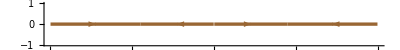

```mathematica
DisplayFlow[CS1,1]
```

The DisplayPhasePortrait command displays the equilibrium points of the system and their stabilities (with blue points being stable and red points being unstable).

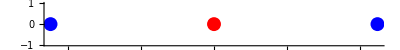

```mathematica
DisplayPhasePortrait[CS1]
```

Various kinds of Dynamica plots can be combined using the standard Show command in Mathematica.

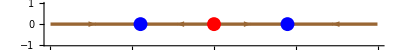

```mathematica
Show[DisplayFlow[CS1,1],DisplayPhasePortrait[CS1]]
```

We can also use Mathematica's Manipulate command to easily create interactively manipulable displays.  Evaluate the following expression to explore the relationship between the zeroes of the vectorfield function, the equilibirum points and the flow in the cubic system as the parameter d is varied.  Note that many standard Mathematica graphics options (such as PlotRange), can be applied to plots created by Dynamcia.

```mathematica
With[{CS1=CS1/.c->0},
Manipulate[
Show[
Plot[dd x-x^3,{x,-5,5}],
DisplayFlow[CS1/.d->dd,5],
DisplayPhasePortrait[CS1/.d->dd],AspectRatio->1,Frame->True,PlotRange->{-10,10}],
{dd,-2,5}]]
```

The DisplayBifurcationDiagram command can be used to construct and display bifurcation diagrams. Here we set d to 5 and display the bifurcation diagram as c is varied.  As before, blue corresponds to stable branches and red corresponds to unstable branches.  Bifurcations are denoted by a black dot and labelled by their type.  Here, "F" denotes a fold or saddle-node bifurcation. If the plot is not as smooth as you would like, the MaxStepSize option can be used to specify a smaller stepsize than the default.

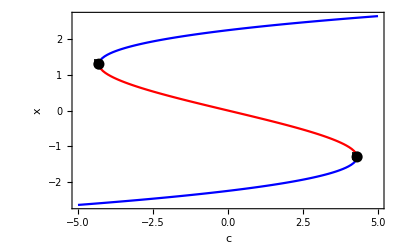

```mathematica
DisplayBifurcationDiagram[CS1,c,MaxStepSize->0.1]
```

Here is another bifurcation diagram with c set to the value we specified at the beginning of this section and varying d. Note the classic pitchfork diagram that occurs, with the branch bifurcation denoted with a "B".

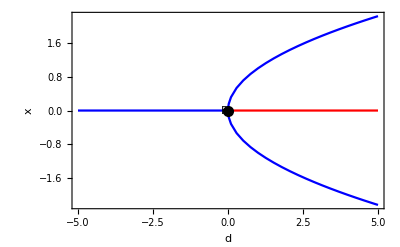

```mathematica
DisplayBifurcationDiagram[CS1,d]
```

Finally, the DisplayParameterChart command can be used to display how the parameter space of a dynamical system is divided into different phase portraits as two parameters are varied. Curves of saddle-node bifurcations are displayed in black. Here we see the classic pair of saddle-node bifurcation curves meeting in a cusp. These curves divide the parameter space of the cubic system into an inner region with bistable dynamics and an outer region with unistable dynamics. Note that the cusp point is not labelled because Dynamica does not explicitly detect such points at present.

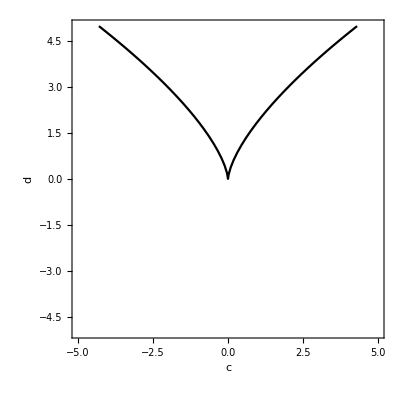

```mathematica
DisplayParameterChart[CS1,{c,d}]
```

## 2D Cubic System

Defining dynamical systems extends straightforwardly to higher dimensions.  Here we define the 2-dimensional dynamical system obtained by coupling two 1-dimensional cubic systems.

 OverDot[x_1]=-x_1^3+d_11 x_1+d_21 x_2 +c_1
OverDot[x_2]=-x_2^3+d_12 x_1+d_22 x_2 +c_2
 
and specify some default values for the six parameters. Note the use of the trailing semicolon to surpress printing of the result.

```mathematica
CS2=DynamicalSystem[
{-x1^3+d11 x1+d21 x2+c1,-x2^3+d22 x2+d12 x1+c2},
{{x1,-5,5},{x2,-5,5}},
{{c1,-2,2},{c2,-2,2},{d11,-2,2},{d12,-2,2},{d21,-2,2},{d22,-2,2}}];
```

### Planar Example 1

```mathematica
CS2a=CS2/.{c1->0,c2->0,d11->1/2,d12->1,d21->1,d22->1/2};
```

The DisplayVectorField command can once again be used.  Note that the option VectorPoints can be used to control how finely the grid of vectors is drawn.

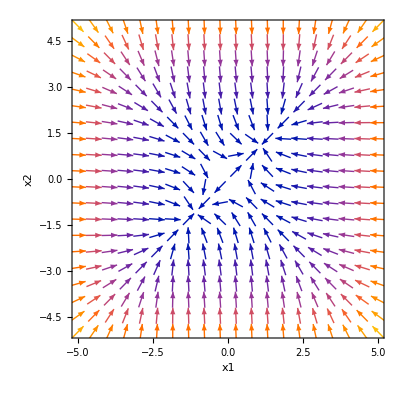

```mathematica
DisplayVectorField[CS2a,VectorPoints->20]
```

The DisplayTrajectories command can also be used on 2-dimensional systems.  By default, one arrow is drawn on each trajectory, but the Arrows option can be used to specify fewer or more.  In addition, the TrajectoryPlotMode option controls how much of the trajectory through each point is displayed. A setting of From  (the default) means that trajectories are integrated from each initial point in forward time only, while a setting of Through means that trajectories are integrated in both forward and backward time from each initial point.  Among the standard Mathematica options that are useful here, the PlotStyle option can be used to specify different colors or line styles for the trajectories.

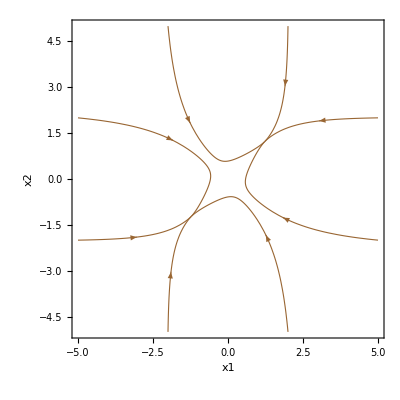

```mathematica
DisplayTrajectories[CS2a,{{-2,-5},{2,-5},{5,-2},{5,2},{2,5},{-2,5},{-5,2},{-5,-2}},5]
```

The DisplayFlow command can also be used on 2-dimensional systems.  Once again, the number of arrows drawn is specified by the  Arrows option. In addition, the PlotPoints option can be used to specify the number of initial conditions to use in the horizontal and vertical directions and the PlotStyle option can be used to specify different colors or line styles for the trajectories. A setting of Grid (the default) for the FlowPlotMode option produces a uniform coverage of the entire state space, but is not always as visually appealing as a setting of Boundary, which only uses initial conditions along the edge of the plot.

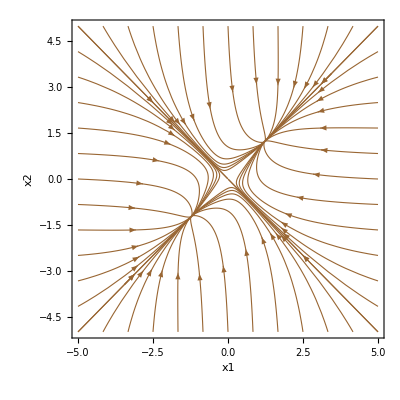

```mathematica
DisplayFlow[CS2a,10,FlowPlotMode->Boundary]
```

The DisplayPhasePortrait command can also be used on 2-dimensional systems.  Green points denote saddle nodes.  The SaddleManifolds option can be used to display the 1-dimensional saddle trajectories of each saddle point.  There are quite a number of options associated with the computation and display of saddle trajectories, including SaddleManifoldInitialStep, SaddleManifoldDuration, SaddleManifoldPlotPoints, and SaddleManifoldStyle and SaddleManifoldArrows. Note that equilibrium points are found by solving for simultaneous zeros of the vectorfield from a number of randomly-generated initial guesses, so not all equilibrium points may be found every time.  To change the number of initial guesses, use the option Tries.

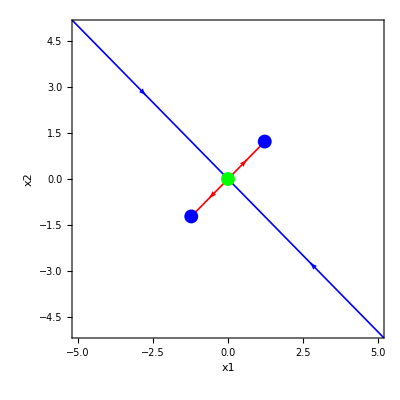

```mathematica
DisplayPhasePortrait[CS2a,SaddleManifolds->True]
```

The global variable $PhasePortraitEPs always contains a list of the equilibrium points found during the last call to  DisplayPhasePortrait.

```mathematica
$PhasePortraitEPs
```

{EquilibriumPoint[Stable,Node,{-1.22474,-1.22474}],EquilibriumPoint[Saddle,Node,{0,0}],EquilibriumPoint[Stable,Node,{1.22474,1.22474}]}

Once again, the various plots produced by Dynamica can be combined using the standard Mathematica command  Show.

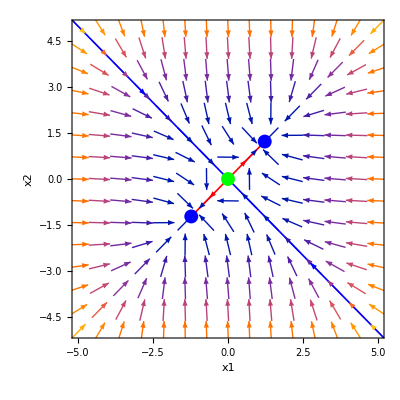

```mathematica
Show[DisplayVectorField[CS2a],DisplayPhasePortrait[CS2a,SaddleManifolds->True]]
```

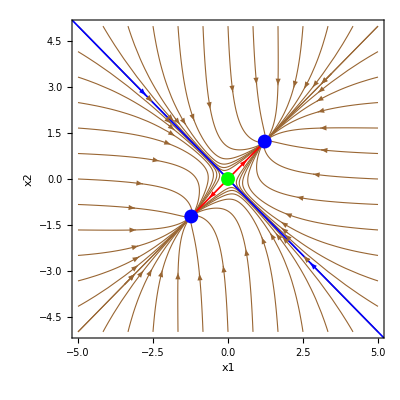

```mathematica
Show[
DisplayFlow[CS2a,5,FlowPlotMode->Boundary],
DisplayPhasePortrait[CS2a,SaddleManifolds->True]]
```

Once again, we can  use Mathematica's Manipulate command to easily create interactively manipulable displays.  Evaluate the following expression to explore how the nullclines and the phase portrait of the system change as the parameters d_11 and d_22 are covaried.  The option NullManifold specifies that the nullclines should be shown. Other options related to the calculation and display of nullclines include NullManifold2PlotPoints and NullManifold2Style.

```mathematica
With[{CS2=CS2a/.{c1->0,c2->0,d12->1,d21->1}},
Manipulate[
DisplayPhasePortrait[
CS2/.{d11->self ,d22->self},NullManifolds->True,NullManifold2PlotPoints->75,Tries->250],
{self,-2,5}]]
```

Bifurcation diagrams for planar systems are produced in the same way as for 1-dimensional systems.  By default, DisplayBifurcationDiagram works by finding the equilibrium points at each end of the parameter range and then following each of them into the interior of the plot, detecting any bifurcations that occur.  You can use the Tries option to change the number of initial guesses used when finding equilibrium points.  Since some branches of equilibria may not reach left or right edges of the parameter range, the options InteriorPoints and InteriorGrid are provided. The InteriorPoints option takes a list of parameter values internal to the parameter range for which to also find equilibrium points and follow them. The  InteriorGrid option takes an integer that specifies the number of uniformly-spaced internal points to use.  For example, a value of 1 specifies the midpoint of the bifurcation parameter's range (in this case, c_1=0). These options are uneccesary for this example.

```mathematica
DisplayBifurcationDiagram[CS2a,c1]
```

-Graphics3D-

By default, planar bifurcation diagrams are displayed as 3-dimensional plots.  However, although 3-dimensional plots can be interactively rotated in Mathematica, it is sometimes clearer to view such diagrams as 2-dimensional plots by projecting out one of the state variables.  The StateVariables option allows you to do this by specifying which of the state variables to plot.

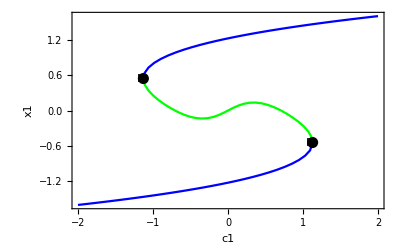

```mathematica
g=DisplayBifurcationDiagram[CS2a,c1,StateVariables->{x1},FrameLabel->None]
```

The global variable $BifurcationDiagramBPs always contains a list of the bifurcation points found during the last call to  DisplayBifurcationDiagram.

```mathematica
$BifurcationDiagramBPs
```

{BifurcationPoint[Fold,{0.54293715298421,1.01683293607948},{c1→-1.12825409027697,c2→0,d11→1/2,d12→1,d21→1,d22→1/2}],BifurcationPoint[Fold,{-0.54293715298421,-1.01683293607948},{c1→1.12825409027697,c2→0,d11→1/2,d12→1,d21→1,d22→1/2}]}

Parameter charts for planar systems are produced in the same way as for 1D systems.

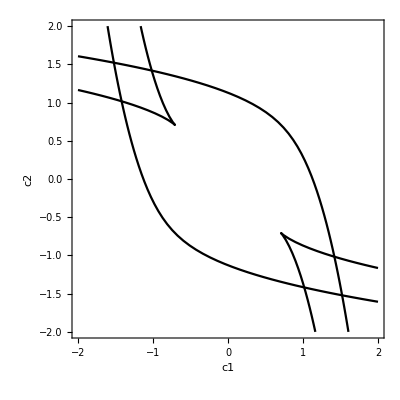

```mathematica
DisplayParameterChart[CS2a,{c1,c2}]
```

### Planar Example 2

We can also find and display limit cycles using Dynamica, although doing so requires a bit more work than for equilibrium points. First, we define a copy of our planar cubic system with different parameters so that it exhibits a limit cycle.

```mathematica
CS2b=CS2a/.{d11->2,d22->2,d21->-1};
```

Now we can use DisplayFlow to verify that a limit cycle exists and to find its approximate location in state space.

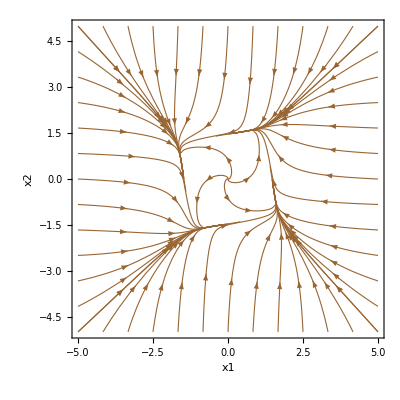

```mathematica
DisplayFlow[CS2b,2,FlowPlotMode->Boundary,Arrows->2,InteriorPoints->{{0.1,0.1},{-0.1,-0.1},{-0.1,0.1},{0.1,-0.1}}]
```

Next, we use  DisplayTrajectories with different initial conditions and durations in order to find a point near the limit cycle and the approximate period of the limit cycle.

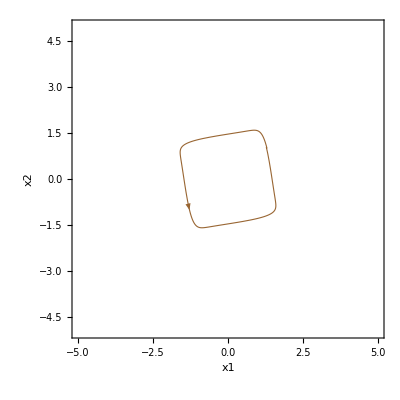

```mathematica
DisplayTrajectories[CS2b,{{1.3,1}},9.55]
```

Now we use the command FindLimitCycle to compute the exact limit cycle using the approximate point and period that we estimated above. Here, we make use of the global variable $Trajectories, which contains a list of each trajectory (which is itself a list of points) computed during the last call to DisplayTrajectories. Note that FindLimitCycle is not always capable of finding a limit cycle unless the intial point and period are extremely accurate.

```mathematica
LC=FindLimitCycle[CS2b,Last[First[$Trajectories]],9.55]
```

LimitCycle[Stable,9.52362,{1.27564,1.04283}]

Finally, we can put put the complete phase portrait together by giving the limit cycle we found to the LimitSets option of DisplayPhasePortrait.

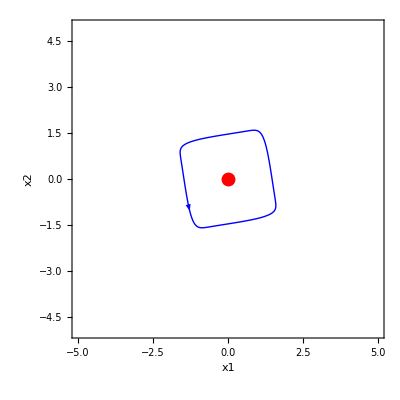

```mathematica
DisplayPhasePortrait[CS2b,LimitSets->{LC},Tries->100]
```

Dynamica has limited support for following branches of limit cycles. We can  follow a branch of limit cycles starting from a given limit cycle in a given parameter using the command FollowLimitCycleBranch. Note that this command can take a while to execute.

```mathematica
LCB=FollowLimitCycleBranch[LC,d11];
```

This limit cycle branch can be displayed in a bifurcation diagram using the LimitCycleBranches option to DisplayBifurcationDiagram.

```mathematica
DisplayBifurcationDiagram[CS2b,d11,LimitCycleBranches->{LCB}]
```

-Graphics3D-

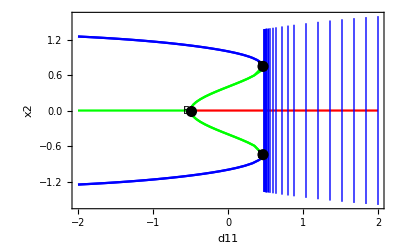

```mathematica
DisplayBifurcationDiagram[CS2b,d11,StateVariables->{x2},LimitCycleBranches->{LCB}]
```

In order to understand the bifurcation that destroys the limit cycle branch, we can extract the d_11value for the leftmost limit cycle in the branch.

```mathematica
DSParameterValue[LSDynamicalSystem[First[LCB]],d11]//N
```

0.48

Then we display the phase portrait for that value of d_11.

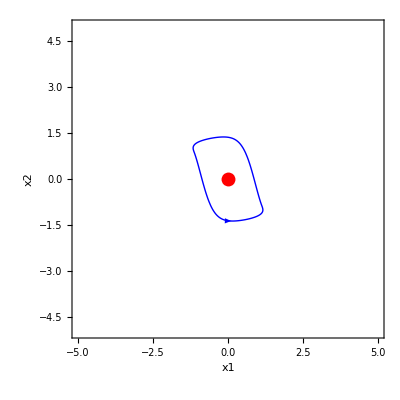

```mathematica
DisplayPhasePortrait[CS2b/.d11->0.48,LimitSets->{First[LCB]},Tries->100]
```

Finally, we display the phase portrait for a slightly smaller value of d_11. We can clearly see that the limit cycle is destroyed by a pair of saddle-node bifurcations on a loop occuring at the "corners" of the limit cycle.

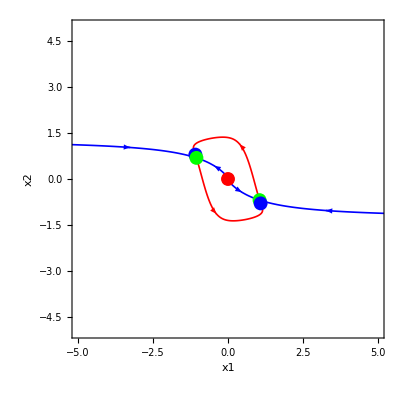

```mathematica
DisplayPhasePortrait[CS2b/.d11->0.45,SaddleManifolds->True,Tries->100]
```

And this displays the entire parameter chart in (c_1, c_2) that contains the above system.  The gray curves denote curves of Hopf bifurcations and "BT" stands for a codimension 2 Bogdanov-Takens bifurcation. The InteriorPoints and InteriorGrid options can be used not only in DisplayBifurcationDiagram, but also in DisplayParameterChart. Here the setting of 1 for InteriorGrid adds an interior point at the center of the plot, which is necessary for finding the Hopf bifurcation curves.

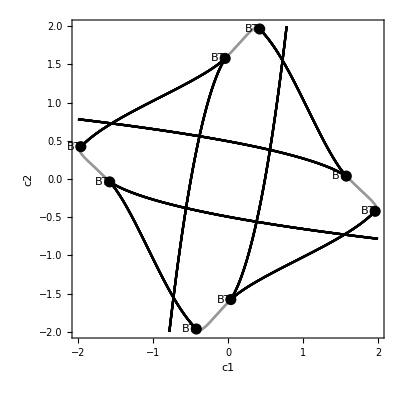

```mathematica
DisplayParameterChart[CS2b,{c1,c2},InteriorGrid->3]
```

The global variable $ParameterChartCodim2BPs always contains a list of the codimension 2 bifurcation points found during the last call to  DisplayParameterChart.

```mathematica
$ParameterChartCodim2BPs
```

{Codim2Point[BogdanovTakens,{0.577350269189626,-1.},{c1→-1.96225044864938,c2→0.422649730810374,d11→2,d12→1,d21→-1,d22→2}],Codim2Point[BogdanovTakens,{1.,-0.577350269189626},{c1→-1.57735026918963,c2→-0.0377495513506237,d11→2,d12→1,d21→-1,d22→2}],Codim2Point[BogdanovTakens,{1.,0.577350269189626},{c1→-0.422649730810374,c2→-1.96225044864938,d11→2,d12→1,d21→-1,d22→2}],Codim2Point[BogdanovTakens,{-0.577350269189626,-1.},{c1→-0.0377495513506238,c2→1.57735026918963,d11→2,d12→1,d21→-1,d22→2}],Codim2Point[BogdanovTakens,{0.577350269189626,1.},{c1→0.0377495513506237,c2→-1.57735026918963,d11→2,d12→1,d21→-1,d22→2}],Codim2Point[BogdanovTakens,{-1.,-0.577350269189626},{c1→0.422649730810374,c2→1.96225044864938,d11→2,d12→1,d21→-1,d22→2}],Codim2Point[BogdanovTakens,{-1.,0.577350269189626},{c1→1.57735026918963,c2→0.0377495513506238,d11→2,d12→1,d21→-1,d22→2}],Codim2Point[BogdanovTakens,{-0.577350269189626,1.},{c1→1.96225044864938,c2→-0.422649730810374,d11→2,d12→1,d21→-1,d22→2}]}

### Planar Example 3

Another example of a planar bifurcation diagram.  This diagram contains a Hopf bifurcation (denoted by the "H").

```mathematica
CS2c=CS2b/.{c2->-0.2,d11->1.1,d22->1.1,d21->-1};
```

```mathematica
DisplayBifurcationDiagram[CS2c,c1]
```

-Graphics3D-

The procedure outlined above can be used to find and follow the branch of limit cycles emanating from the Hopf point. Let's start at c_1=0.

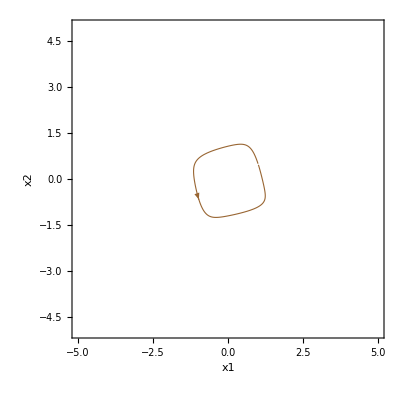

```mathematica
DisplayTrajectories[CS2c/.c1->0,{{1,0.5}},7.1]
```

```mathematica
LC=FindLimitCycle[CS2c,Last[First[$Trajectories]],7.1]
```

LimitCycle[Stable,7.12967,{1.01327,0.464586}]

```mathematica
LCB=FollowLimitCycleBranch[LC,c1];
```

```mathematica
DisplayBifurcationDiagram[CS2c,c1,LimitCycleBranches->{LCB}]
```

-Graphics3D-

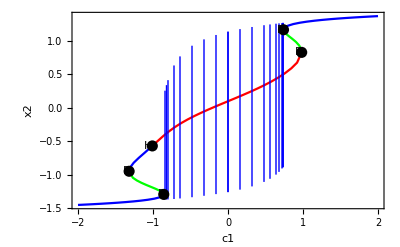

```mathematica
DisplayBifurcationDiagram[CS2c,c1,StateVariables->{x2},LimitCycleBranches->{LCB},FrameLabel->None]
```

Hmm... There is a branch of limit cycles, but it is created and destroyed in saddle-node bifurcations on a loop.  Let's try a c_1 value closer to the Hopf point. For greater accuracy, we first integrate for a long time until we have a point that is very near the limit cycle.

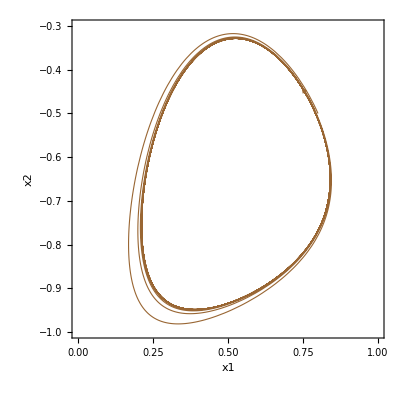

```mathematica
DisplayTrajectories[CS2c/.c1->-0.98,{{0.8,-0.5}},100,PlotRange->{{0,1},{-1,-0.3}}]
```

We can access that point using the global variable $Trajectories.

```mathematica
Last[First[$Trajectories]]
```

{0.493581,-0.330611}

Finally, we use the above initial point to estimate the period.

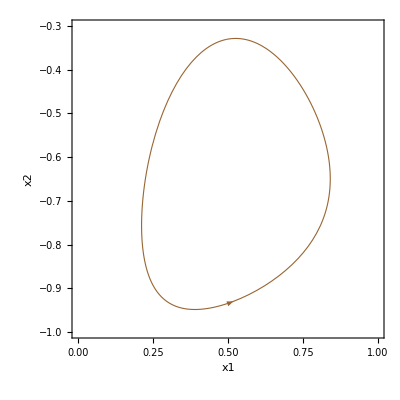

```mathematica
DisplayTrajectories[CS2c/.c1->-0.98,{{0.4935806946128592,-0.33061112963715905}},7,PlotRange->{{0,1},{-1,-0.3}}]
```

OK, now we find another limit cycle.

```mathematica
LC2=FindLimitCycle[CS2c/.c1->-0.98,Last[First[$Trajectories]],7]
```

LimitCycle[Stable,7.00171,{0.493968,-0.330554}]

Let's follow this new branch. Note that we need to specify a sufficiently small MaxStepSize for FollowLimitCycleBranch to work.

```mathematica
LCB2=FollowLimitCycleBranch[LC2,c1,MaxStepSize->0.01];
```

And here is the final bifurcation diagram that we construct.  The Hopf bifurcation gives rise to a branch of stable limit cycles that quickly terminates in a homoclinic bifurcation (when the limit cycle touches the green branch of saddle point branch).  In addition, another branch of stable limit cycles exists between the two innermost fold bifurcations. This branch is created and destroyed in saddle-node bifurcations on a loop.

```mathematica
DisplayBifurcationDiagram[CS2c,c1,LimitCycleBranches->{LCB,LCB2}]
```

-Graphics3D-

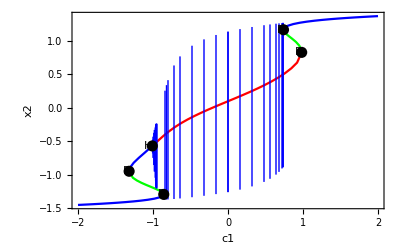

```mathematica
DisplayBifurcationDiagram[CS2c,c1,StateVariables->{x2},LimitCycleBranches->{LCB,LCB2},FrameLabel->None]
```

Here is the phase portrait at the approximate location of the homoclinic bifurcation.

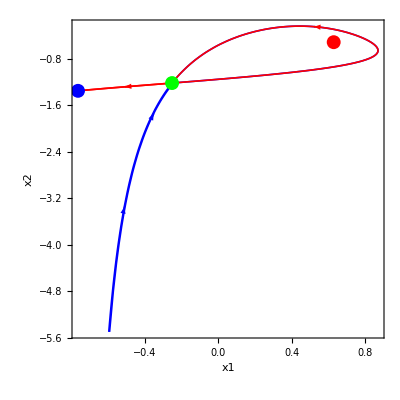

```mathematica
DisplayPhasePortrait[CS2c/.c1->-0.952525487,SaddleManifolds->True,Tries->250,PlotRange->Automatic]
```

### Planar Example 4

When there is too much symmetry in a system, it may not be possible for a command to successfully complete.  Here is an example in our planar cubic system where the codimension of a bifurcation is too high for Dynamica to follow with the given number of parameters.

```mathematica
CS2d=CS2/.{d11->1/2,d12->1,d21->1,d22->1/2,c1->0,c2->0};
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {x1,x2,d12,d21}={0,0,-2,-0.125}

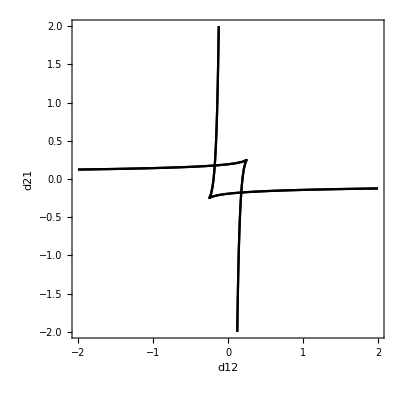

```mathematica
DisplayParameterChart[CS2d,{d12,d21}]
```

By breaking the symmetry, we can can lower the codimension and allow Dynamica to proceed.

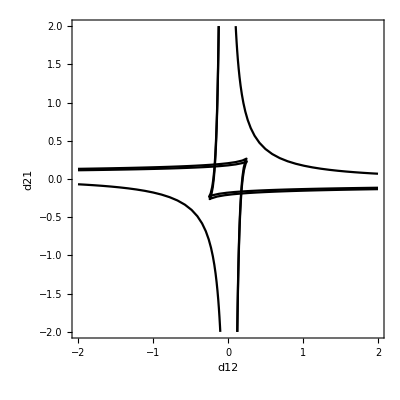

```mathematica
DisplayParameterChart[CS2d/.c1->0.01,{d12,d21}]
```

## 3D Cubic System

Most of the capabilities of Dynamica generalize in the obvious way to 3-dimensional systems. Here we use the 3-dimensional dynamical system obtained by coupling three 1-dimensional cubic systems as our example.

 OverDot[x_1]=-x_1^3+d_11 x_1+d_21 x_2 +d_31 x_3 +c_1
OverDot[x_2]=-x_2^3+d_12 x_1+d_22 x_2 +d_32 x_3+c_2
OverDot[x_3]=-x_3^3+d_13 x_1+d_23 x_2 +d_33 x_3+c_2

```mathematica
CS3=DynamicalSystem[
{-x1^3+d11 x1+d21 x2+d31 x3+c1,
-x2^3+d12 x1+d22 x2+d32 x3+c2,
-x3^3+d13 x1+d23 x2+d33 x3+c3},
{{x1,-5,5},{x2,-5,5},{x3,-5,5}},
{{c1,-2,2},{c2,-2,2},{c3,-2,2},
{d11,-2,2},{d12,-2,2},{d13,-2,2},
{d21,-2,2},{d22,-2,2},{d23,-2,2},
{d31,-2,2},{d32,-2,2},{d33,-2,2}}];
```

```mathematica
CS3=CS3/.{c1->0,c2->0,c3->0,d11->1/2,d12->1,d13->1,d21->1,d22->1/2,d23->1,d31->1,d32->1,d33->1/2};
```

```mathematica
DisplayVectorField[CS3]
```

-Graphics3D-

```mathematica
DisplayTrajectories[CS3,{{-5,-5,-5},{5,-5,-5},{-5,-5,5},{-5,5,-5},{-5,5,5},{5,-5,5},{5,5,-5},{5,5,5}},5]
```

-Graphics3D-

```mathematica
DisplayFlow[CS3,5,FlowPlotMode->Boundary]
```

-Graphics3D-

Because the null manifolds of a 3-dimensional system are surfaces, there are a number of new options available for displaying them.  First, besides True and False, the NullManifolds option can also take a list of boolean values that specify whether or not each of the three null manifolds should be shown.  In addition, the opacity of the null manifolds can be controlled using the NullManifoldOpacity option. Finally, the number of points to use in each direction when plotting null manifolds can be specified using the NullManifolds3PlotPoints option.

```mathematica
DisplayPhasePortrait[CS3,NullManifolds->{True,False,True},NullManifoldOpacity->0.5]
```

-Graphics3D-

Only 1-dimensional saddle manifolds are currently plotted in Dynamica, even though 2-dimensional saddle manifolds exist in 3-dimensional systems as well.

```mathematica
DisplayPhasePortrait[CS3,SaddleManifolds->True]
```

-Graphics3D-

Because a bifurcation diagram of a 3-dimensional dynamical system would be 4-dimensional, by default  Dynamica displays only the first state variable.  You can specify another state variable or pair of state variables to use with the StateVariables option.

```mathematica
DisplayBifurcationDiagram[CS3,d12,StateVariables->{x1,x3}]
```

-Graphics3D-

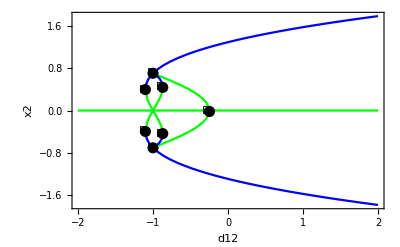

```mathematica
DisplayBifurcationDiagram[CS3,d12,StateVariables->{x2}]
```

The parameter charts for higher-dimensional dynamical systems can become quite complex.  The following chart exhibits not only Bogdanov-Takens (BT) points, but also Fold-Hopf (FH) points and another pair of codimension 2 points that Dynamica cannot currently classify.

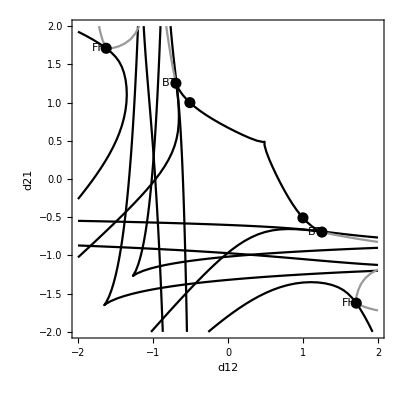

```mathematica
DisplayParameterChart[CS3/.{c1->0.25,c2->0.25},{d12,d21}]
```

## Beyond 3-Dimensional Dynamics

In principle, Dynamica can work with dynamical systems of any dimension.  However, displaying the dynamics of such systems becomes problematic for dimension greater than three.  Here is Rössler's hyperchaotic system.

```mathematica
DS=DynamicalSystem[
{-y-z,x+a y+w,b+x z,-c z+d w},
{{x,-100,25},{y,-100,50},{z,-25,250},{w,-200,200}},
{{a,-1,1},{b,-3,3},{c,-1,1},{d,-1,1}}]/.{a->0.25,b->3,c->0.5,d->0.05};
```

Vector fields of higher-dimensional systems cannot be displayed.

```mathematica
DisplayVectorField[DS]
```

Dimension must be ≤ 3 for DisplayVectorField

The trajectories of higher-dimensional systems can be displayed using the StateVariables option to select which state variables to show. Note that we need a long duration to really show the hyperchaotic attractor and a lot of plot points to make the curve smooth.

```mathematica
DisplayTrajectories[DS,{{-10,-6,0,10}},250,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1,1},StateVariables->{x,y,z},Arrows->0]
```

-Graphics3D-

The flows of higher-dimensional systems cannot be displayed.

```mathematica
DisplayFlow[DS,100]
```

Dimension must be ≤ 3 for DisplayFlow

The phase portraits of higher-dimensional systems can be displayed using the StateVariables option to select which state variables to show. 1-dimensional saddle manifolds of higher-dimensional saddle points can also be displayed.  However, null manifolds cannot be displayed for higher-dimensional systems.

```mathematica
DisplayPhasePortrait[DS,StateVariables->{x,y,z},SaddleManifolds->True,SaddleManifoldDuration->500,SaddleManifoldPlotPoints->500]
```

-Graphics3D-

In order to get a sense of how the 1-dimensional saddle manifolds relate to the hyperchaotic attractor, we can put together the phase portrait with our earlier trajectory plot. This plot really needs to be interactively rotated in 3D to see what's going on.

```mathematica
Show[DisplayPhasePortrait[DS,StateVariables->{x,y,z},SaddleManifolds->True,SaddleManifoldDuration->500,SaddleManifoldPlotPoints->500],DisplayTrajectories[DS,{{-10,-6,0,10}},250,MaxSteps->15000,PlotPoints->20000,PlotRange->Automatic,StateVariables->{x,y,z},Arrows->0]]
```

-Graphics3D-

Displaying bifurcation diagrams works with higher-dimensional systems using the StateVariables option. Note that the saddle points head off to ±∞ as c approaches 0.

```mathematica
DisplayBifurcationDiagram[DS,c,MaxSteps->350,StateVariables->{x,y},PlotRange->All]
```

Warning: MaxSteps exceeded, terminating branch

Warning: MaxSteps exceeded, terminating branch

-Graphics3D-

Displaying parameter charts also works with higher-dimensional systems.

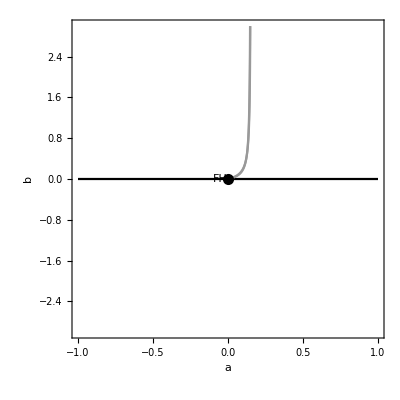

```mathematica
DisplayParameterChart[DS,{a,b},MaxSteps->250]
```

## State-Space Transformations of Dynamical Systems

It is sometimes convenient to be able to symbolically transform a dynamical system from one coordinate system to another.  The Dynamica command TransformDynamicalSystem provides this capability.

Consder the following planar dynamical system, which represents a simple 2-neuron continuous-time recurrent neural network (CTRNN) in state space.

```mathematica
σ[x_]=1/(1+ⅇ^-x);
```

```mathematica
CTRNN2y=
DynamicalSystem[
{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2])/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-16,16},{y2,-16,16}},
{{w11,-16,16},{w12,-16,16},{w21,-16,16},{w22,-16,16},{θ1,-16,16},{θ2,-16,16},{τ1,0.5,10},{τ2,0.5,10}}];
```

```mathematica
CTRNN2y=CTRNN2y/.{w11->10,w12->2,w21->-3,w22->11,θ1->-4,θ2->-6.5,τ1->1,τ2->1};
```

We can display the phase portrait of this particular 2-neuron CTRNN in the usual way.

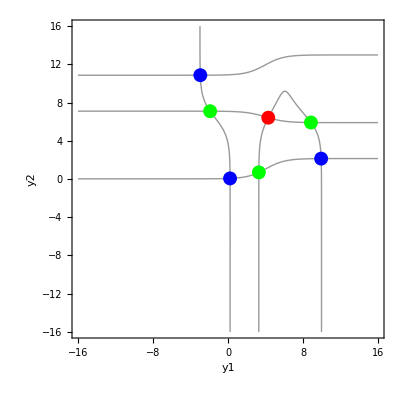

```mathematica
DisplayPhasePortrait[CTRNN2y,NullManifolds->True,Tries->100]
```

It is sometimes convenient to study such systems in output or activation space, represented by the coordinate transformations y_i↦σ(y_i+θ_i). TransformDynamicalSystem works by taking a dynamical system, a list of new state variables and ranges for them, and a list of transformations relating the new state variables to the old.  In this case, we must specify ranges that are slightly greater than 0 and slightly less than 1, since σ(.) can only reach these limits at ±∞. Mathematica warns that it must use inverse functions to algebraically solve for the new differential equations, so that some solutions may be lost.  In this case, there is no problem.

```mathematica
With[{ε=10^-5},
CTRNN2o=
TransformDynamicalSystem[CTRNN2y,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
```

Now we can display the phase portrait of the same 2-neuron CTRNN in output space.

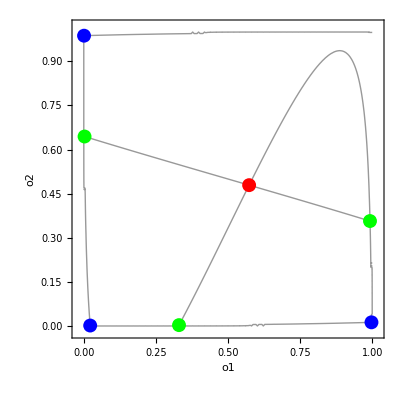

```mathematica
DisplayPhasePortrait[CTRNN2o,Tries->100,NullManifolds->True,PlotRange->{{-0.02,1.02},{-0.02,1.02}}]
```

We can use some internal Dynamica functions to see how the differential equations have been symbolically transformed from the state space (y_1,y_2) to the output space (o_1,o_2).

```mathematica
Dynamica`Private`DSFunctions[CTRNN2y]
```

{(w11/(1+ⅇ^(-y1-θ1))+w21/(1+ⅇ^(-y2-θ2))-y1)/τ1,(w12/(1+ⅇ^(-y1-θ1))+w22/(1+ⅇ^(-y2-θ2))-y2)/τ2}

```mathematica
Dynamica`Private`DSFunctions[CTRNN2o]
```

{-((-1+o1) o1 (o1 w11+o2 w21+θ1-Log[-o1/(-1+o1)]))/τ1,-((-1+o2) o2 (o1 w12+o2 w22+θ2-Log[-o2/(-1+o2)]))/τ2}